```mathematica
(*The primaries are 1,ϵ,X,Y,Z1,Z2,σ1,σ2*)
n=30;
p=6;
p'=5;
cv=1-6(p-p')^2/(p p')//Echo[#,"c = "]&;
hv[r_,s_]:=((p r - p' s)^2-(p - p')^2)/(4 p p');
sv[a_,b_]:=2 (2/(p p'))^(1/2)(-1)^(1 + a[[2]]b[[1]]+a[[1]] b[[2]])Sin[π p/p' a[[1]] b[[1]]]Sin[π p'/p a[[2]] b[[2]]] ;
tv[a_,e_:1]:=ⅇ^(2 π ⅈ e(hv[a[[1]],a[[2]]]-cv/24));
ηv[a_]:=(-1)^(a[[1]]+1);
Nv[a_]:=2(-1)^a[[1]] Cos[(π a[[1]])/4];
H=Join[Flatten[Table[{r, s}, {r, 1, Floor[(p'-1)/2]}, {s, 1, p-1}], 1], If[EvenQ[p'], Table[{p'/2, s}, {s, 1, Floor[(p-1)/2]}], {}]];
h = hv @@@ H;
H //Echo[#,"(r,s): "]&;
h //Echo[#,"h = "]&;
s=Outer[sv, H,H,1]//Simplify;
z={
{1,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,2,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{1,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,1},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,2,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,1}
};
t=DiagonalMatrix[tv/@H];
```

c =   4/5

(r,s):   {{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3},{2,4},{2,5}}

h =   {0,1/8,2/3,13/8,3,2/5,1/40,1/15,21/40,7/5}

```mathematica
(*Now we will select some Kac Labels because we don't have access to all of them here*)
s1=Outer[sv, H,H,1]//Simplify;
s2=(((I {{x,y},{y,-x}})/.y->Sqrt[1-x^2])/.x->(-Sqrt[2/(5+Sqrt[5])]))//Simplify;
u = {
{1,0,0,0,0,0,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,0,0,0},
{0,0,1/√2,0,0,0,0,0,0,0,1/√2,0},
{0,0,0,1,0,0,0,0,0,0,0,0},
{0,0,0,0,1,0,0,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,0,0,0},
{0,0,0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,1/√2,0,0,0,1/√2},
{0,0,0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,0,0,0,0,1,0,0},
{0,0,1/√2,0,0,0,0,0,0,0,-1/√2,0},
{0,0,0,0,0,0,0,1/√2,0,0,0,-1/√2}
} ;
S=u.ArrayFlatten[{{s1,0},{0,s2}}].u;(* /Sqrt[2/(5+Sqrt[5])] //Simplify//MatrixForm*)
T=DiagonalMatrix[tv /@( H~Join~{{1,3},{2,3}})];
Z={{1,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1}};
```

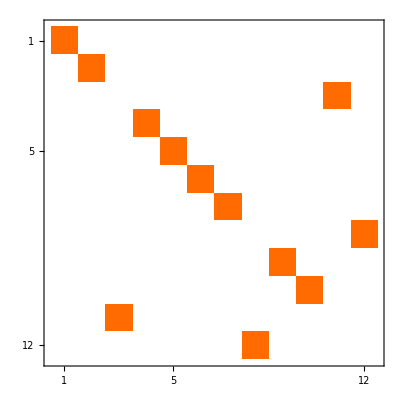

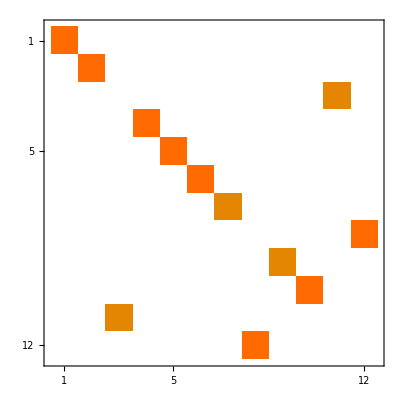

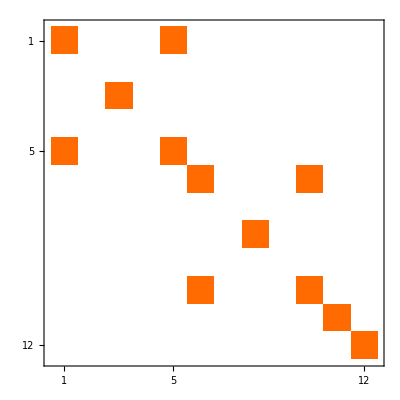

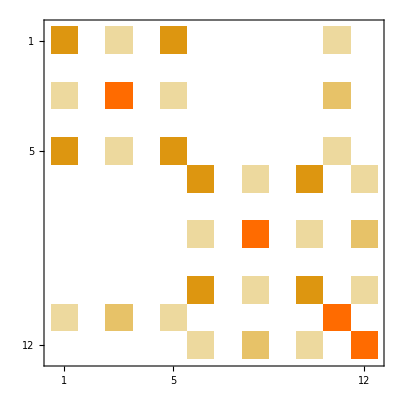

```mathematica
S.S//N//Chop//MatrixPlot
S.T.S.T.S.T //N//Chop//MatrixPlot
ConjugateTranspose[T].Z.T//N//Chop //MatrixPlot
ConjugateTranspose[S].Z.(S)//N//Chop// MatrixPlot
```

```mathematica
(# / First[#] &) /@ s //FullSimplify//MatrixForm
```

(1 | √3 | 2 | √3 | 1 | 1/2 (1+√5) | √(3/2 (3+√5)) | 1+√5 | √(3/2 (3+√5)) | 1/2 (1+√5)
1 | -1 | 0 | 1 | -1 | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 1/2 (-1-√5) | 1/2 (1+√5)
1 | 0 | -1 | 0 | 1 | 1/2 (1+√5) | 0 | 1/2 (-1-√5) | 0 | 1/2 (1+√5)
1 | 1 | 0 | -1 | -1 | 1/2 (-1-√5) | 1/2 (-1-√5) | 0 | 1/2 (1+√5) | 1/2 (1+√5)
1 | -√3 | 2 | -√3 | 1 | 1/2 (1+√5) |  | 1+√5 |  | 1/2 (1+√5)
1 | -√3 | 2 | -√3 | 1 | 1/2 (1-√5) |  | 1-√5 |  | 1/2 (1-√5)
1 | 1 | 0 | -1 | -1 | 1/2 (-1+√5) | 1/2 (-1+√5) | 0 | 1/2 (1-√5) | 1/2 (1-√5)
1 | 0 | -1 | 0 | 1 | 1/2 (1-√5) | 0 | 1/2 (-1+√5) | 0 | 1/2 (1-√5)
1 | -1 | 0 | 1 | -1 | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 1/2 (-1+√5) | 1/2 (1-√5)
1 | √3 | 2 | √3 | 1 | 1/2 (1-√5) |  | 1-√5 |  | 1/2 (1-√5))

```mathematica
(*T={{Exp[2Pi I (2/3 - c/24)],0},{0,Exp[2Pi I (1/15 - c/24)]}};
Y=I {{x,y},{y,-x}}/.y->Sqrt[1-x^2];
Y/.x->(-Sqrt[2/(5+Sqrt[5])])//Simplify//MatrixForm
Y.Y/.x->(-Sqrt[2/(5+Sqrt[5])])//Simplify//MatrixForm
FullSimplify[(Y.T.Y.T.Y.T)] //MatrixForm
FullSimplify[((Y.T.Y.T.Y.T))/.x->(-Sqrt[2/(5+Sqrt[5])])] //MatrixForm*)
```

# -------- Modular Bootstrap -----------

```mathematica
s=If[True,{{Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,40] (5-5^Rational[1,2]),Rational[1,2] 10^Rational[-1,2],Rational[-1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,4] 5^Rational[-1,2],Rational[1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,2] 10^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[-1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[1,2] 5^Rational[-1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2]},{Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,40] (5-5^Rational[1,2]),Rational[1,2] 10^Rational[-1,2],Rational[-1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,4] 5^Rational[-1,2],Rational[1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,2] 10^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[-1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[1,2] 5^Rational[-1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2]},{Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[-1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[1,40] (5+5^Rational[1,2]),Rational[1,2] 10^Rational[-1,2],Rational[-1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[-1,4] 5^Rational[-1,2],Rational[1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[1,2] 10^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[-1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[-1,2] 5^Rational[-1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2]},{Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[-1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[1,40] (5+5^Rational[1,2]),Rational[1,2] 10^Rational[-1,2],Rational[-1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[-1,4] 5^Rational[-1,2],Rational[1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[1,2] 10^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[-1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[-1,2] 5^Rational[-1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2]},{Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[-1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[1,40] (5+5^Rational[1,2]),Rational[-1,2] 10^Rational[-1,2],Rational[1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[-1,4] 5^Rational[-1,2],Rational[-1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[-1,2] 10^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[-1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[-1,2] 5^Rational[-1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2]},{Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[-1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[1,40] (5+5^Rational[1,2]),Rational[-1,2] 10^Rational[-1,2],Rational[1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[-1,4] 5^Rational[-1,2],Rational[-1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[-1,2] 10^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[-1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[-1,2] 5^Rational[-1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2]},{Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,40] (5-5^Rational[1,2]),Rational[-1,2] 10^Rational[-1,2],Rational[1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,4] 5^Rational[-1,2],Rational[-1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[-1,2] 10^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[-1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[1,2] 5^Rational[-1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2]},{Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5+5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,80] (5-5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,40] (5-5^Rational[1,2]),Rational[-1,2] 10^Rational[-1,2],Rational[1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,4] 5^Rational[-1,2],Rational[-1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[-1,2] 10^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[-1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[1,2] 5^Rational[-1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2]},{Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),0,0,0,0,Rational[1,2] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[1,20] (-5-5^Rational[1,2]),0,0,Rational[1,20] (-5+5^Rational[1,2]),Rational[-1,2] 5^Rational[-1,2],0,0,Rational[1,2] 5^Rational[-1,2],0,0,0,0,0,Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],0,0,0,0},{Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),0,0,0,0,Rational[1,2] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[1,20] (-5-5^Rational[1,2]),0,0,Rational[1,20] (-5+5^Rational[1,2]),Rational[-1,2] 5^Rational[-1,2],0,0,Rational[1,2] 5^Rational[-1,2],0,0,0,0,0,Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],0,0,0,0},{Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),0,0,0,0,Rational[-1,2] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,20] (-5+5^Rational[1,2]),0,0,Rational[1,20] (-5-5^Rational[1,2]),Rational[1,2] 5^Rational[-1,2],0,0,Rational[-1,2] 5^Rational[-1,2],0,0,0,0,0,Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],0,0,0,0},{Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),0,0,0,0,Rational[-1,2] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,20] (-5+5^Rational[1,2]),0,0,Rational[1,20] (-5-5^Rational[1,2]),Rational[1,2] 5^Rational[-1,2],0,0,Rational[-1,2] 5^Rational[-1,2],0,0,0,0,0,Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],0,0,0,0},{Rational[1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,2] 2^Rational[-1,2],0,Rational[-1,2] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],0,Rational[-1,2] 2^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],0,Rational[-1,2] 2^Rational[-1,2],Rational[1,2] 2^Rational[-1,2],0,Rational[-1,2] 5^Rational[-1,2],0,0,0,0,0,0,0,0,0,0,0,0},{Rational[1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],10^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],-10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],-10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],10^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],0,0,0,0,0,0,0,0,0,0,0,0},{Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,20] (-5-5^Rational[1,2]),Rational[1,20] (-5-5^Rational[1,2]),Rational[1,20] (-5+5^Rational[1,2]),Rational[1,20] (-5+5^Rational[1,2]),Rational[1,2] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,20] (5-5^Rational[1,2]),0,0,Rational[1,20] (5+5^Rational[1,2]),Rational[1,2] 5^Rational[-1,2],0,0,Rational[1,2] 5^Rational[-1,2],0,0,0,0,-5^Rational[-1,2],0,0,0,0,0,0,0,0,0,0,0,0},{Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],0,0,0,0,Rational[1,2] 2^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],0,Rational[1,20] (5+5^Rational[1,2]),Rational[1,2] 5^Rational[-1,2],0,Rational[-1,2] 10^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,20] (5-5^Rational[1,2]),Rational[-1,2] 2^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[1,20] (-5+5^Rational[1,2]),Rational[1,20] (-5-5^Rational[1,2]),Rational[-1,2] 5^Rational[-1,2],0,0,0,0,0,0,0,0,0,0,0,0,0},{Rational[-1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[-1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[-1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[-1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),0,0,0,0,0,10^Rational[-1,2],0,Rational[1,2] 5^Rational[-1,2],Rational[1,20] (5-5^Rational[1,2]),0,-10^Rational[-1,2],Rational[1,20] (-5-5^Rational[1,2]),Rational[-1,2] 5^Rational[-1,2],0,Rational[1,20] (5+5^Rational[1,2]),Rational[1,2] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[1,20] (-5+5^Rational[1,2]),0,0,0,0,0,0,0,0,0,0,0,0,0},{Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5-5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,40] (5+5^Rational[1,2]),Rational[1,20] (-5+5^Rational[1,2]),Rational[1,20] (-5+5^Rational[1,2]),Rational[1,20] (-5-5^Rational[1,2]),Rational[1,20] (-5-5^Rational[1,2]),Rational[-1,2] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[1,20] (5+5^Rational[1,2]),0,0,Rational[1,20] (5-5^Rational[1,2]),Rational[-1,2] 5^Rational[-1,2],0,0,Rational[-1,2] 5^Rational[-1,2],0,0,0,0,5^Rational[-1,2],0,0,0,0,0,0,0,0,0,0,0,0},{Rational[1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],-10^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],-10^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],0,0,0,0,0,0,0,0,0,0,0,0},{Rational[1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[-1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[-1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[-1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[-1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),0,0,0,0,0,-10^Rational[-1,2],0,Rational[1,2] 5^Rational[-1,2],Rational[1,20] (-5-5^Rational[1,2]),0,10^Rational[-1,2],Rational[1,20] (5-5^Rational[1,2]),Rational[-1,2] 5^Rational[-1,2],0,Rational[1,20] (-5+5^Rational[1,2]),Rational[1,2] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[1,20] (5+5^Rational[1,2]),0,0,0,0,0,0,0,0,0,0,0,0,0},{Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],0,0,0,0,Rational[-1,2] 2^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],0,Rational[1,20] (5-5^Rational[1,2]),Rational[-1,2] 5^Rational[-1,2],0,Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[1,20] (5+5^Rational[1,2]),Rational[1,2] 2^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,20] (-5-5^Rational[1,2]),Rational[1,20] (-5+5^Rational[1,2]),Rational[1,2] 5^Rational[-1,2],0,0,0,0,0,0,0,0,0,0,0,0,0},{Rational[1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[-1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[-1,2] 2^Rational[-1,2],0,Rational[-1,2] 5^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],0,Rational[1,2] 2^Rational[-1,2],Rational[1,4] 5^Rational[-1,2],0,Rational[1,2] 2^Rational[-1,2],Rational[-1,2] 2^Rational[-1,2],0,Rational[-1,2] 5^Rational[-1,2],0,0,0,0,0,0,0,0,0,0,0,0},{Rational[1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[-1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[-1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[-1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[-1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),0,0,0,0,0,-10^Rational[-1,2],0,Rational[-1,2] 5^Rational[-1,2],Rational[1,20] (5+5^Rational[1,2]),0,10^Rational[-1,2],Rational[1,20] (-5+5^Rational[1,2]),Rational[1,2] 5^Rational[-1,2],0,Rational[1,20] (5-5^Rational[1,2]),Rational[-1,2] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,20] (-5-5^Rational[1,2]),0,0,0,0,0,0,0,0,0,0,0,0,0},{Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],0,0,0,0,Rational[-1,2] 2^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],0,Rational[1,20] (-5+5^Rational[1,2]),Rational[1,2] 5^Rational[-1,2],0,Rational[-1,2] 10^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,20] (-5-5^Rational[1,2]),Rational[1,2] 2^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[1,20] (5+5^Rational[1,2]),Rational[1,20] (5-5^Rational[1,2]),Rational[-1,2] 5^Rational[-1,2],0,0,0,0,0,0,0,0,0,0,0,0,0},{Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 10^Rational[-1,2],0,0,0,0,Rational[1,2] 2^Rational[-1,2],Rational[1,2] 10^Rational[-1,2],0,Rational[1,20] (-5-5^Rational[1,2]),Rational[-1,2] 5^Rational[-1,2],0,Rational[-1,2] 10^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[1,20] (-5+5^Rational[1,2]),Rational[-1,2] 2^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,20] (5-5^Rational[1,2]),Rational[1,20] (5+5^Rational[1,2]),Rational[1,2] 5^Rational[-1,2],0,0,0,0,0,0,0,0,0,0,0,0,0},{Rational[-1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[-1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[-1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[-1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,20] 2^Rational[-1,2] (5+5^Rational[1,2]),Rational[1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),Rational[1,20] 2^Rational[-1,2] (-5+5^Rational[1,2]),0,0,0,0,0,10^Rational[-1,2],0,Rational[-1,2] 5^Rational[-1,2],Rational[1,20] (-5+5^Rational[1,2]),0,-10^Rational[-1,2],Rational[1,20] (5+5^Rational[1,2]),Rational[1,2] 5^Rational[-1,2],0,Rational[1,20] (-5-5^Rational[1,2]),Rational[-1,2] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,20] (5-5^Rational[1,2]),0,0,0,0,0,0,0,0,0,0,0,0,0},{Rational[1,2] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[-1,2] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],0,0,0,0,Rational[-1,2] 5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],-5^Rational[-1,2],0,0,5^Rational[-1,2],Rational[1,2] 5^Rational[-1,2],0,0,Rational[-1,2] 5^Rational[-1,2],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Rational[-1,40] (-1)^Rational[23,40] (1+(-1)^Rational[1,4]) (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,40] (-1)^Rational[23,40] (1+(-1)^Rational[1,4]) (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,4] (-1)^Rational[27,40] 5^Rational[-1,2] (1-(-1)^Rational[1,4]-(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[1,4] (-1)^Rational[3,40] 5^Rational[-1,2] (-1+(-1)^Rational[1,4]-(-1)^Rational[3,5]+(-1)^Rational[17,20]),Rational[1,4] (-1)^Rational[7,40] 5^Rational[-1,2] (-1-(-1)^Rational[1,4]+(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[-1,4] (-1)^Rational[7,40] 5^Rational[-1,2] (-1-(-1)^Rational[1,4]+(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[1,40] (-1)^Rational[3,40] (-1+(-1)^Rational[1,4]) (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[-1,40] (-1)^Rational[3,40] (-1+(-1)^Rational[1,4]) (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),0,0,0,0},{Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Rational[1,40] (-1)^Rational[23,40] (1+(-1)^Rational[1,4]) (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[-1,40] (-1)^Rational[23,40] (1+(-1)^Rational[1,4]) (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,4] (-1)^Rational[3,40] 5^Rational[-1,2] (-1+(-1)^Rational[1,4]-(-1)^Rational[3,5]+(-1)^Rational[17,20]),Rational[1,4] (-1)^Rational[27,40] 5^Rational[-1,2] (1-(-1)^Rational[1,4]-(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[-1,4] (-1)^Rational[7,40] 5^Rational[-1,2] (-1-(-1)^Rational[1,4]+(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[1,4] (-1)^Rational[7,40] 5^Rational[-1,2] (-1-(-1)^Rational[1,4]+(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[-1,40] (-1)^Rational[3,40] (-1+(-1)^Rational[1,4]) (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,40] (-1)^Rational[3,40] (-1+(-1)^Rational[1,4]) (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),0,0,0,0},{Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Rational[1,4] (-1)^Rational[27,40] 5^Rational[-1,2] (1-(-1)^Rational[1,4]-(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[1,4] (-1)^Rational[3,40] 5^Rational[-1,2] (-1+(-1)^Rational[1,4]-(-1)^Rational[3,5]+(-1)^Rational[17,20]),Rational[1,40] (-1)^Rational[31,40] (1+(-1)^Rational[1,4]) (-5-5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[-1,40] (-1)^Rational[31,40] (1+(-1)^Rational[1,4]) (-5-5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,40] (-1)^Rational[11,40] (-1+(-1)^Rational[1,4]) (-5-5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[-1,40] (-1)^Rational[11,40] (-1+(-1)^Rational[1,4]) (-5-5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[-1,4] (-1)^Rational[7,40] 5^Rational[-1,2] (-1-(-1)^Rational[1,4]+(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[1,4] (-1)^Rational[7,40] 5^Rational[-1,2] (-1-(-1)^Rational[1,4]+(-1)^Rational[2,5]+(-1)^Rational[13,20]),0,0,0,0},{Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Rational[1,4] (-1)^Rational[3,40] 5^Rational[-1,2] (-1+(-1)^Rational[1,4]-(-1)^Rational[3,5]+(-1)^Rational[17,20]),Rational[1,4] (-1)^Rational[27,40] 5^Rational[-1,2] (1-(-1)^Rational[1,4]-(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[-1,40] (-1)^Rational[31,40] (1+(-1)^Rational[1,4]) (-5-5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,40] (-1)^Rational[31,40] (1+(-1)^Rational[1,4]) (-5-5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[-1,40] (-1)^Rational[11,40] (-1+(-1)^Rational[1,4]) (-5-5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,40] (-1)^Rational[11,40] (-1+(-1)^Rational[1,4]) (-5-5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,4] (-1)^Rational[7,40] 5^Rational[-1,2] (-1-(-1)^Rational[1,4]+(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[-1,4] (-1)^Rational[7,40] 5^Rational[-1,2] (-1-(-1)^Rational[1,4]+(-1)^Rational[2,5]+(-1)^Rational[13,20]),0,0,0,0},{Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Rational[1,4] (-1)^Rational[7,40] 5^Rational[-1,2] (-1-(-1)^Rational[1,4]+(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[-1,4] (-1)^Rational[7,40] 5^Rational[-1,2] (-1-(-1)^Rational[1,4]+(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[1,40] (-1)^Rational[11,40] (-1+(-1)^Rational[1,4]) (-5-5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[-1,40] (-1)^Rational[11,40] (-1+(-1)^Rational[1,4]) (-5-5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[-1,40] (-1)^Rational[31,40] (1+(-1)^Rational[1,4]) (-5-5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,40] (-1)^Rational[31,40] (1+(-1)^Rational[1,4]) (-5-5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,4] (-1)^Rational[27,40] 5^Rational[-1,2] (1-(-1)^Rational[1,4]-(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[1,4] (-1)^Rational[3,40] 5^Rational[-1,2] (-1+(-1)^Rational[1,4]-(-1)^Rational[3,5]+(-1)^Rational[17,20]),0,0,0,0},{Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Rational[-1,4] (-1)^Rational[7,40] 5^Rational[-1,2] (-1-(-1)^Rational[1,4]+(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[1,4] (-1)^Rational[7,40] 5^Rational[-1,2] (-1-(-1)^Rational[1,4]+(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[-1,40] (-1)^Rational[11,40] (-1+(-1)^Rational[1,4]) (-5-5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,40] (-1)^Rational[11,40] (-1+(-1)^Rational[1,4]) (-5-5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,40] (-1)^Rational[31,40] (1+(-1)^Rational[1,4]) (-5-5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[-1,40] (-1)^Rational[31,40] (1+(-1)^Rational[1,4]) (-5-5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,4] (-1)^Rational[3,40] 5^Rational[-1,2] (-1+(-1)^Rational[1,4]-(-1)^Rational[3,5]+(-1)^Rational[17,20]),Rational[1,4] (-1)^Rational[27,40] 5^Rational[-1,2] (1-(-1)^Rational[1,4]-(-1)^Rational[2,5]+(-1)^Rational[13,20]),0,0,0,0},{Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Rational[1,40] (-1)^Rational[3,40] (-1+(-1)^Rational[1,4]) (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[-1,40] (-1)^Rational[3,40] (-1+(-1)^Rational[1,4]) (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[-1,4] (-1)^Rational[7,40] 5^Rational[-1,2] (-1-(-1)^Rational[1,4]+(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[1,4] (-1)^Rational[7,40] 5^Rational[-1,2] (-1-(-1)^Rational[1,4]+(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[1,4] (-1)^Rational[27,40] 5^Rational[-1,2] (1-(-1)^Rational[1,4]-(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[1,4] (-1)^Rational[3,40] 5^Rational[-1,2] (-1+(-1)^Rational[1,4]-(-1)^Rational[3,5]+(-1)^Rational[17,20]),Rational[1,40] (-1)^Rational[23,40] (1+(-1)^Rational[1,4]) (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[-1,40] (-1)^Rational[23,40] (1+(-1)^Rational[1,4]) (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),0,0,0,0},{Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5+5^Rational[1,2]))^Rational[1,2],Rational[1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (Rational[1,10] (5-5^Rational[1,2]))^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Rational[-1,40] (-1)^Rational[3,40] (-1+(-1)^Rational[1,4]) (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,40] (-1)^Rational[3,40] (-1+(-1)^Rational[1,4]) (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,4] (-1)^Rational[7,40] 5^Rational[-1,2] (-1-(-1)^Rational[1,4]+(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[-1,4] (-1)^Rational[7,40] 5^Rational[-1,2] (-1-(-1)^Rational[1,4]+(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[1,4] (-1)^Rational[3,40] 5^Rational[-1,2] (-1+(-1)^Rational[1,4]-(-1)^Rational[3,5]+(-1)^Rational[17,20]),Rational[1,4] (-1)^Rational[27,40] 5^Rational[-1,2] (1-(-1)^Rational[1,4]-(-1)^Rational[2,5]+(-1)^Rational[13,20]),Rational[-1,40] (-1)^Rational[23,40] (1+(-1)^Rational[1,4]) (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,40] (-1)^Rational[23,40] (1+(-1)^Rational[1,4]) (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),0,0,0,0},{Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Rational[-1,20] (-1)^Rational[9,10] (5+5 (-1)^Rational[2,5]+5^Rational[1,2]-(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,20] (-1)^Rational[9,10] (5+5 (-1)^Rational[2,5]+5^Rational[1,2]-(-1)^Rational[2,5] 5^Rational[1,2]),Rational[-1,2] (-1)^Rational[3,10] 5^Rational[-1,2] (-1+(-1)^Rational[2,5]),Rational[1,2] (-1)^Rational[3,10] 5^Rational[-1,2] (-1+(-1)^Rational[2,5])},{Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Rational[1,20] (-1)^Rational[9,10] (5+5 (-1)^Rational[2,5]+5^Rational[1,2]-(-1)^Rational[2,5] 5^Rational[1,2]),Rational[-1,20] (-1)^Rational[9,10] (5+5 (-1)^Rational[2,5]+5^Rational[1,2]-(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,2] (-1)^Rational[3,10] 5^Rational[-1,2] (-1+(-1)^Rational[2,5]),Rational[-1,2] (-1)^Rational[3,10] 5^Rational[-1,2] (-1+(-1)^Rational[2,5])},{Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Rational[-1,2] (-1)^Rational[3,10] 5^Rational[-1,2] (-1+(-1)^Rational[2,5]),Rational[1,2] (-1)^Rational[3,10] 5^Rational[-1,2] (-1+(-1)^Rational[2,5]),Rational[1,20] (-1)^Rational[7,10] (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[-1,20] (-1)^Rational[7,10] (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2])},{Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1+5^Rational[-1,2])^Rational[1,2],Rational[-1,4] (1-5^Rational[-1,2])^Rational[1,2],Rational[1,4] (1-5^Rational[-1,2])^Rational[1,2],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Rational[1,2] (-1)^Rational[3,10] 5^Rational[-1,2] (-1+(-1)^Rational[2,5]),Rational[-1,2] (-1)^Rational[3,10] 5^Rational[-1,2] (-1+(-1)^Rational[2,5]),Rational[-1,20] (-1)^Rational[7,10] (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2]),Rational[1,20] (-1)^Rational[7,10] (5+5 (-1)^Rational[2,5]-5^Rational[1,2]+(-1)^Rational[2,5] 5^Rational[1,2])}},If[34594144980401276046===$SessionID,Out[42],Message[MessageName[Syntax,"noinfoker"]];Missing["NotAvailable"];Null]];
```

```mathematica
i={{{1,1},{1,1},1},{{1,1},{1,1},-1},{{1,2},{1,2},1},{{1,2},{1,2},-1},{{1,3},{1,3},1},{{1,3},{1,3},-1},{{1,4},{1,4},1},{{1,4},{1,4},-1},{{2,2},{2,2},1},{{2,2},{2,2},-1},{{2,4},{2,4},1},{{2,4},{2,4},-1},{{1,1},{1,2},0},{{1,1},{1,3},0},{{1,1},{1,4},0},{{1,1},{2,2},0},{{1,1},{2,4},0},{{1,2},{1,3},0},{{1,2},{1,4},0},{{1,2},{2,2},0},{{1,2},{2,4},0},{{1,3},{1,4},0},{{1,3},{2,2},0},{{1,3},{2,4},0},{{1,4},{2,2},0},{{1,4},{2,4},0},{{2,2},{2,4},0},{{1,1},{1,1},2},{{1,1},{1,1},-2},{{1,2},{1,2},2},{{1,2},{1,2},-2},{{1,3},{1,3},2},{{1,3},{1,3},-2},{{1,4},{1,4},2},{{1,4},{1,4},-2},{{2,2},{2,2},2},{{2,2},{2,2},-2},{{2,4},{2,4},2},{{2,4},{2,4},-2}};
z=Outer[(KroneckerDelta[#1,#2] + KroneckerDelta[#1[[1]],#2[[1]]]KroneckerDelta[#1[[2]],#2[[2]]]KroneckerDelta[#1[[3]],-#2[[3]]])(1-KroneckerDelta[Abs[#1[[3]]],2])(1-KroneckerDelta[Abs[#2[[3]]],2])&,i,i,1];
```

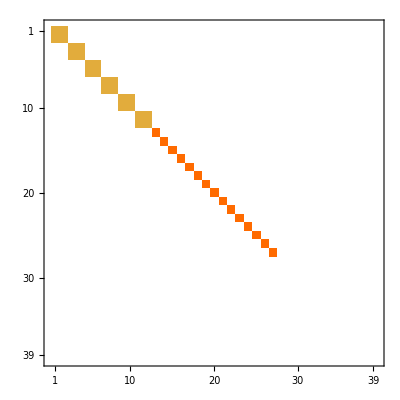

```mathematica
z//MatrixPlot
nz=Position[z, _?(# ≠0 &)];
X=Array[x,Length[nz]];
m=Conjugate[s] . ReplacePart[z,Thread[nz->X]] . s  //Flatten;
A=CoefficientArrays[Thread[m==0],X][[2]]//Simplify//Normal;
a=(A[[#,All]]&/@(Flatten[FirstPosition[#,1]&/@ RowReduce[Transpose[Chop[N[A]]]]]) )//FullSimplify;
```

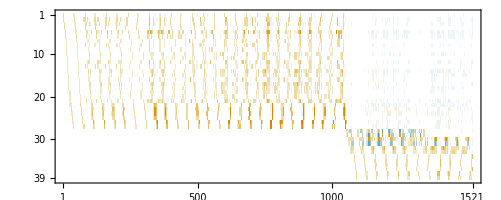

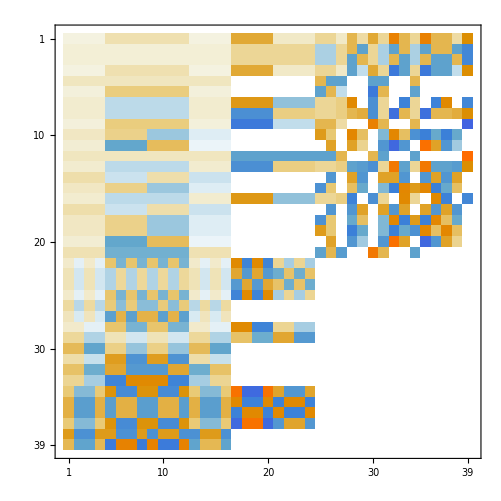

```mathematica
Transpose[N[A]]//RowReduce//MatrixPlot
a//MatrixPlot
```

```mathematica
b=Inverse[N[a]]//Chop;
b=RootApproximant/@b;
y=b.X//Simplify;
m=N[ConjugateTranspose[s] . ReplacePart[z,Thread[nz->y]] . s] ;
```

```mathematica
ClearDenominators[e_]:=Module[{l,r,L},
l=e[[1]];
r=e[[2]];
L=LCM@@(Level[List@@#,1]&/@Flatten[{l,r}]//Flatten//Denominator);
e[[0]][L*(l-r)//ExpandAll,0]
];
eqn=(# ≥ 0 & /@(m//Flatten)) //Expand//Chop//Rationalize//Expand// DeleteDuplicates;
eqn=ClearDenominators/@eqn;
eqn//MatrixForm
```

(x[1]≥0
x[2]≥0
x[3]≥0
x[4]≥0
x[5]≥0
x[6]≥0
x[7]≥0
x[8]≥0
x[9]≥0
x[10]≥0
x[11]≥0
x[12]≥0
x[13]≥0
x[14]≥0
x[15]≥0
x[16]≥0
x[17]≥0
x[18]≥0
x[19]≥0
x[20]≥0
x[21]≥0
x[22]≥0
x[23]≥0
x[24]≥0
x[25]≥0
x[26]≥0
x[27]≥0
x[1]+x[3]+x[8]≥0
x[2]+x[4]+x[13]≥0
x[5]+x[6]+x[21]≥0
x[7]+x[12]≥0
2 x[2]+x[13]≥0
x[14]+x[15]≥0
x[7]+x[9]+x[12]+x[16]≥0
2 x[3]+x[8]≥0
x[10]+x[11]+x[17]+x[18]≥0
x[10]+x[17]≥0
x[12]+x[16]≥0
x[14]+x[15]+x[19]+x[20]≥0
x[14]+x[19]≥0
x[17]+x[18]≥0
2 x[5]+x[21]≥0
x[22]+x[24]≥0
2 x[23]+x[25]≥0
x[22]+2 x[24]≥0
x[23]+x[25]≥0
2 x[26]+x[27]≥0
x[26]+x[27]≥0
x[1]+x[2]+x[3]+x[4]+x[7]+x[8]+x[9]+x[12]+x[13]+x[16]≥0
x[2]+x[3]+x[12]≥0
2 x[5]≥0
x[10]+x[14]+x[17]+x[19]≥0
x[14]+x[17]≥0
2 x[5]+2 x[6]+2 x[21]≥0
x[10]+x[11]+x[14]+x[15]+x[17]+x[18]+x[19]+x[20]≥0
x[14]+x[15]+x[17]+x[18]≥0
2 x[2]+2 x[3]+x[7]+x[8]+2 x[12]+x[13]+x[16]≥0
x[22]+x[23]+x[24]+x[25]≥0
x[22]+2 x[23]+2 x[24]+x[25]≥0
4 x[26]+2 x[27]≥0
2 x[26]+2 x[27]≥0
x[1]+x[4]+x[9]≥0
2 x[6]≥0
x[15]+x[18]≥0
x[11]+x[20]≥0
x[10]+x[19]≥0
x[7]+x[8]+x[13]+x[16]≥0
x[22]+x[25]≥0
x[23]+x[24]≥0
2 x[26]≥0
2 x[27]≥0
2 x[1]+2 x[2]+x[8]≥0
x[7]+x[9]+x[12]≥0
x[8]+x[13]≥0
x[10]+x[11]+x[14]≥0
x[10]+x[15]≥0
2 x[2]+2 x[3]+x[8]+x[13]≥0
x[9]+x[12]+x[16]≥0
x[10]+x[14]+x[15]+x[17]≥0
x[11]+x[14]+x[18]≥0
2 x[3]+2 x[4]+x[13]≥0
x[14]+x[17]+x[18]+x[19]≥0
x[15]+x[17]+x[20]≥0
x[17]+x[19]+x[20]≥0
x[18]+x[19]≥0
2 x[5]+2 x[6]+x[21]≥0
2 x[23]≥0
2 x[22]+2 x[24]≥0
2 x[23]+2 x[25]≥0
2 x[24]≥0
2 x[1]+2 x[3]+x[8]≥0
x[7]+x[16]≥0
x[10]+x[11]+x[17]≥0
x[10]+x[18]≥0
x[7]+2 x[12]+x[16]≥0
2 x[2]+2 x[4]+x[13]≥0
2 x[14]+x[15]+x[19]≥0
x[14]+x[15]+x[20]≥0
x[10]+2 x[17]+x[18]≥0
x[11]+x[17]+x[18]≥0
x[14]+x[19]+x[20]≥0
x[15]+x[19]≥0
2 x[1]+2 x[4]≥0
2 x[2]+2 x[3]≥0
2 x[21]≥0
2 x[25]≥0
2 x[22]≥0
2 x[1]+2 x[5]+x[7]+x[8]+x[9]≥0
x[7]+x[8]+x[21]≥0
2 x[2]+2 x[5]+x[7]+x[12]+x[13]+x[21]≥0
2 x[2]+2 x[6]+x[12]+x[21]≥0
2 x[3]+2 x[5]+x[8]+x[12]+x[16]+x[21]≥0
2 x[3]+2 x[6]+x[12]+x[21]≥0
2 x[4]+2 x[5]+x[9]+x[13]+x[16]≥0
x[13]+x[16]+x[21]≥0
x[11]+x[14]+x[15]+x[17]+x[18]+x[20]≥0
2 x[22]+2 x[23]+2 x[24]+2 x[25]≥0
2 x[23]+2 x[24]≥0
2 x[1]+2 x[6]+x[9]≥0
2 x[2]+2 x[5]+x[12]≥0
x[7]+x[13]+x[21]≥0
2 x[3]+2 x[5]+x[12]≥0
x[8]+x[16]+x[21]≥0
2 x[4]+2 x[6]+x[9]≥0
x[10]+x[15]+x[18]+x[19]≥0
2 x[22]+2 x[25]≥0
2 x[1]+2 x[2]+2 x[3]+2 x[4]+2 x[8]+2 x[13]≥0
4 x[5]+2 x[21]≥0
2 x[22]+4 x[24]≥0
4 x[23]+2 x[25]≥0
2 x[1]+2 x[3]+2 x[5]+2 x[6]+x[7]+2 x[8]+x[9]+x[12]+x[16]+2 x[21]≥0
2 x[3]+2 x[5]+x[7]+x[8]+x[12]+x[21]≥0
2 x[2]+2 x[4]+2 x[5]+2 x[6]+x[7]+x[9]+x[12]+2 x[13]+x[16]+2 x[21]≥0
2 x[2]+2 x[5]+x[12]+x[13]+x[16]+x[21]≥0
x[10]+2 x[14]+x[15]+2 x[17]+x[18]+x[19]≥0
2 x[22]+4 x[23]+4 x[24]+2 x[25]≥0
2 x[1]+2 x[5]+x[8]+x[9]+x[16]≥0
2 x[4]+2 x[5]+x[7]+x[9]+x[13]≥0
x[10]+x[11]+x[14]+x[17]+x[19]+x[20]≥0
2 x[1]+2 x[2]+2 x[3]+2 x[4]+x[7]+x[8]+2 x[9]+2 x[12]+x[13]+x[16]≥0
4 x[26]+4 x[27]≥0
4 x[26]≥0
x[28]≥0
x[29]≥0
x[30]≥0
x[31]≥0
2 x[28]-2 x[29]+2 x[30]-2 x[31]≥0
-2 x[28]+2 x[29]≥0
-2 x[28]+2 x[31]≥0
x[32]≥0
x[33]≥0
-2 x[29]+2 x[30]≥0
x[32]+x[33]≥0
2 x[30]-2 x[31]≥0
x[34]≥0
x[35]≥0
x[36]≥0
x[37]≥0
x[38]≥0
x[39]≥0
x[28]-x[29]+x[30]-x[31]≥0
x[28]-2 x[29]+2 x[30]-x[31]≥0
2 x[30]-x[31]≥0
x[30]-x[31]≥0
2 x[29]≥0
-2 x[28]+4 x[29]≥0
2 x[32]+x[33]≥0
2 x[30]≥0
x[34]+x[36]≥0
x[35]+x[37]≥0
x[38]+x[39]≥0
-x[28]+x[29]≥0
-x[28]+2 x[29]≥0
2 x[28]-4 x[29]+4 x[30]-2 x[31]≥0
-x[28]+x[31]≥0
-x[29]+x[30]≥0
2 x[28]≥0
x[32]≥0
2 x[32]+x[33]≥0
4 x[30]-2 x[31]≥0
2 x[32]+2 x[33]≥0
x[34]+x[35]+x[36]+x[37]≥0
x[35]+x[36]≥0
x[33]≥0
x[32]+x[33]≥0
2 x[31]≥0
2 x[32]≥0
x[34]+x[37]≥0)

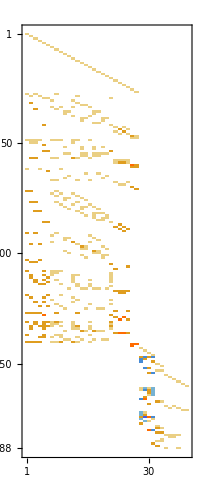

```mathematica
B=Table[Coefficient[eqn[[i]][[1]],X],{i,Length[eqn]}];
B//MatrixPlot
```

```mathematica
isRedundant[A_,i_]:=Module[{rest,n,sol},n=Dimensions[A][[2]];
rest=Delete[A,i];

(*Minimize A[[i]].x subject to:rest.x>=0 x>=0 Sum[x]=1 (normalization to avoid trivial x=0)*)
sol=LinearProgramming[
A[[i]],(*minimize A[[i]].x*)
Append[rest,Table[1,n]],(*constraint matrix*)
Append[Table[{0,1},Length[rest]],{1,0}],(* >=0,then=1*)
Table[{0,Infinity},n] (*x>=0*)];
(*Redundant if minimum value is>=0*)
NumberQ[First@sol]&&A[[i]].sol>=0
]
essential=Select[Range[Length[B]],!isRedundant[B,#]&];
B[[essential]]//MatrixPlot
```

-Graphics-

```mathematica
<<math4ti2`
basis =zsolve[#>=0&/@Flatten[B.X]][[2]];
basis//MatrixForm
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Map[GCD@@#&,basis]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
d=b. # &/@basis //Simplify;
d//Transpose//MatrixForm
```

(1 | 1/2 (3+√5) | 1/2 (3+√5) | 1 | 3+√5 | 2 | 1/2 (1+√5) | 1/2 (1+√5) | 1 | √(3+√5) | √2 | 1/2 (3+√5) | 1/2 (1+√5) | √(7+3 √5) | √(3+√5) | 1/2 (1+√5) | √(7+3 √5) | √(3+√5) | √(3+√5) | √2 | 1+√5 | √(2 (5+√5)) | 2 √(5+2 √5) | 2 √(5+2 √5) | √(2 (5+√5)) | 2 √(10+4 √5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5)+ | 2 √(5+2 √5) | 2 √(5+2 √5)+ | √(10+4 √5) | √(5+√5) | 1 | 1/2 (1+√5) | 1/2 (1+√5) | 1 | √(3+√5) | √2
1 | 1/2 (3+√5) | 1/2 (3+√5) | 1 | 3+√5 | 2 | 1/2 (1+√5) | 1/2 (1+√5) | 1 | √(3+√5) | √2 | 1/2 (3+√5) | 1/2 (1+√5) | √(7+3 √5) | √(3+√5) | 1/2 (1+√5) | √(7+3 √5) | √(3+√5) | √(3+√5) | √2 | 1+√5 | -√(2 (5+√5)) | -2 √(5+2 √5) | -2 √(5+2 √5) | -√(2 (5+√5)) | -2 √(10+4 √5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5)+ | 2 √(5+2 √5) | 2 √(5+2 √5)+ | √(10+4 √5) | √(5+√5) | -1 | 1/2 (-1-√5) | 1/2 (-1-√5) | -1 | -√(3+√5) | -√2
1 | 1/2 (3+√5) | 1/2 (3+√5) | 1 | 3+√5 | 2 | 1/2 (1+√5) | 1/2 (1+√5) | 1 | √(3+√5) | √2 | 1/2 (3+√5) | 1/2 (1+√5) | √(7+3 √5) | √(3+√5) | 1/2 (1+√5) | √(7+3 √5) | √(3+√5) | √(3+√5) | √2 | 1+√5 | √(2 (5+√5)) | 2 √(5+2 √5) | 2 √(5+2 √5) | √(2 (5+√5)) | 2 √(10+4 √5) | 2 √(5+√5) | -2 √(5+2 √5) | √(10-2 √5)-2 √(5+2 √5) | -2 √(5+2 √5) | √(10-2 √5)-2 √(5+2 √5) | -√(10+4 √5) | -√(5+√5) | -1 | 1/2 (-1-√5) | 1/2 (-1-√5) | -1 | -√(3+√5) | -√2
1 | 1/2 (3+√5) | 1/2 (3+√5) | 1 | 3+√5 | 2 | 1/2 (1+√5) | 1/2 (1+√5) | 1 | √(3+√5) | √2 | 1/2 (3+√5) | 1/2 (1+√5) | √(7+3 √5) | √(3+√5) | 1/2 (1+√5) | √(7+3 √5) | √(3+√5) | √(3+√5) | √2 | 1+√5 | -√(2 (5+√5)) | -2 √(5+2 √5) | -2 √(5+2 √5) | -√(2 (5+√5)) | -2 √(10+4 √5) | -2 √(5+√5) | -2 √(5+2 √5) | √(10-2 √5)-2 √(5+2 √5) | -2 √(5+2 √5) | √(10-2 √5)-2 √(5+2 √5) | -√(10+4 √5) | -√(5+√5) | 1 | 1/2 (1+√5) | 1/2 (1+√5) | 1 | √(3+√5) | √2
1 | 1/2 (3-√5) | 1/2 (3-√5) | 1 | 3-√5 | 2 | 1/2 (1-√5) | 1/2 (1-√5) | 1 | √(3-√5) | -√2 | 1/2 (3-√5) | 1/2 (1-√5) | -√(7-3 √5) | √(3-√5) | 1/2 (1-√5) | -√(7-3 √5) | √(3-√5) | √(3-√5) | -√2 | 1-√5 | √(10-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | √(10-2 √5) | 2 √(10-4 √5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5)+√(2 (5+√5)) | -2 √(5-2 √5) | -2 √(5-2 √5)+√(2 (5+√5)) | √(10-4 √5) | -√(5-√5) | 1 | 1/2 (1-√5) | 1/2 (1-√5) | 1 | √(3-√5) | -√2
1 | 1/2 (3-√5) | 1/2 (3-√5) | 1 | 3-√5 | 2 | 1/2 (1-√5) | 1/2 (1-√5) | 1 | √(3-√5) | -√2 | 1/2 (3-√5) | 1/2 (1-√5) | -√(7-3 √5) | √(3-√5) | 1/2 (1-√5) | -√(7-3 √5) | √(3-√5) | √(3-√5) | -√2 | 1-√5 |  | 2 √(5-2 √5) | 2 √(5-2 √5) |  | -2 √(10-4 √5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5)+√(2 (5+√5)) | -2 √(5-2 √5) | -2 √(5-2 √5)+√(2 (5+√5)) | √(10-4 √5) | -√(5-√5) | -1 | 1/2 (-1+√5) | 1/2 (-1+√5) | -1 |  | √2
1 | 1/2 (3-√5) | 1/2 (3-√5) | 1 | 3-√5 | 2 | 1/2 (1-√5) | 1/2 (1-√5) | 1 | √(3-√5) | -√2 | 1/2 (3-√5) | 1/2 (1-√5) | -√(7-3 √5) | √(3-√5) | 1/2 (1-√5) | -√(7-3 √5) | √(3-√5) | √(3-√5) | -√2 | 1-√5 | √(10-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | √(10-2 √5) | 2 √(10-4 √5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5)-√(2 (5+√5)) | 2 √(5-2 √5) | 2 √(5-2 √5)-√(2 (5+√5)) |  | √(5-√5) | -1 | 1/2 (-1+√5) | 1/2 (-1+√5) | -1 |  | √2
1 | 1/2 (3-√5) | 1/2 (3-√5) | 1 | 3-√5 | 2 | 1/2 (1-√5) | 1/2 (1-√5) | 1 | √(3-√5) | -√2 | 1/2 (3-√5) | 1/2 (1-√5) | -√(7-3 √5) | √(3-√5) | 1/2 (1-√5) | -√(7-3 √5) | √(3-√5) | √(3-√5) | -√2 | 1-√5 |  | 2 √(5-2 √5) | 2 √(5-2 √5) |  | -2 √(10-4 √5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5)-√(2 (5+√5)) | 2 √(5-2 √5) | 2 √(5-2 √5)-√(2 (5+√5)) |  | √(5-√5) | 1 | 1/2 (1-√5) | 1/2 (1-√5) | 1 | √(3-√5) | -√2
1 | 1/2 (3-√5) | 1/2 (3-√5) | 1 | 3-√5 | 2 | 1/2 (1-√5) | 1/2 (1-√5) | 1 |  | √2 | 1/2 (3-√5) | 1/2 (1-√5) | √(7-3 √5) |  | 1/2 (1-√5) | √(7-3 √5) |  |  | √2 | 1-√5 | √(10-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | √(10-2 √5) | -2 √(10-4 √5) | 2 √(5-√5) |  | √(2 (5+√5))+ |  | √(2 (5+√5))+ |  | √(5-√5) | 1 | 1/2 (1-√5) | 1/2 (1-√5) | 1 |  | √2
1 | 1/2 (3-√5) | 1/2 (3-√5) | 1 | 3-√5 | 2 | 1/2 (1-√5) | 1/2 (1-√5) | 1 |  | √2 | 1/2 (3-√5) | 1/2 (1-√5) | √(7-3 √5) |  | 1/2 (1-√5) | √(7-3 √5) |  |  | √2 | 1-√5 |  | 2 √(5-2 √5) | 2 √(5-2 √5) |  | 2 √(10-4 √5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5)+√(2 (5+√5)) | -2 √(5-2 √5) | -2 √(5-2 √5)+√(2 (5+√5)) |  | √(5-√5) | -1 | 1/2 (-1+√5) | 1/2 (-1+√5) | -1 | √(3-√5) | -√2
1 | 1/2 (3-√5) | 1/2 (3-√5) | 1 | 3-√5 | 2 | 1/2 (1-√5) | 1/2 (1-√5) | 1 |  | √2 | 1/2 (3-√5) | 1/2 (1-√5) | √(7-3 √5) |  | 1/2 (1-√5) | √(7-3 √5) |  |  | √2 | 1-√5 | √(10-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | √(10-2 √5) | -2 √(10-4 √5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5)-√(2 (5+√5)) | 2 √(5-2 √5) | 2 √(5-2 √5)-√(2 (5+√5)) | √(10-4 √5) | -√(5-√5) | -1 | 1/2 (-1+√5) | 1/2 (-1+√5) | -1 | √(3-√5) | -√2
1 | 1/2 (3-√5) | 1/2 (3-√5) | 1 | 3-√5 | 2 | 1/2 (1-√5) | 1/2 (1-√5) | 1 |  | √2 | 1/2 (3-√5) | 1/2 (1-√5) | √(7-3 √5) |  | 1/2 (1-√5) | √(7-3 √5) |  |  | √2 | 1-√5 |  |  | 2 √(5-2 √5) |  | 2 √(10-4 √5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5)-√(2 (5+√5)) | 2 √(5-2 √5) | 2 √(5-2 √5)-√(2 (5+√5)) | √(10-4 √5) | -√(5-√5) | 1 | 1/2 (1-√5) | 1/2 (1-√5) | 1 |  | √2
1 | 1/2 (3+√5) | 1/2 (3+√5) | 1 | 3+√5 | 2 | 1/2 (1+√5) | 1/2 (1+√5) | 1 | -√(3+√5) | -√2 | 1/2 (3+√5) | 1/2 (1+√5) | -√(7+3 √5) | -√(3+√5) | 1/2 (1+√5) | -√(7+3 √5) | -√(3+√5) | -√(3+√5) | -√2 | 1+√5 | √(2 (5+√5)) | 2 √(5+2 √5) | 2 √(5+2 √5) | √(2 (5+√5)) | -2 √(10+4 √5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5)+ | 2 √(5+2 √5) | 2 √(5+2 √5)+ | -√(10+4 √5) | -√(5+√5) | 1 | 1/2 (1+√5) | 1/2 (1+√5) | 1 | -√(3+√5) | -√2
1 | 1/2 (3+√5) | 1/2 (3+√5) | 1 | 3+√5 | 2 | 1/2 (1+√5) | 1/2 (1+√5) | 1 | -√(3+√5) | -√2 | 1/2 (3+√5) | 1/2 (1+√5) | -√(7+3 √5) | -√(3+√5) | 1/2 (1+√5) | -√(7+3 √5) | -√(3+√5) | -√(3+√5) | -√2 | 1+√5 | -√(2 (5+√5)) | -2 √(5+2 √5) | -2 √(5+2 √5) | -√(2 (5+√5)) | 2 √(10+4 √5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5)+ | 2 √(5+2 √5) | 2 √(5+2 √5)+ | -√(10+4 √5) | -√(5+√5) | -1 | 1/2 (-1-√5) | 1/2 (-1-√5) | -1 | √(3+√5) | √2
1 | 1/2 (3+√5) | 1/2 (3+√5) | 1 | 3+√5 | 2 | 1/2 (1+√5) | 1/2 (1+√5) | 1 | -√(3+√5) | -√2 | 1/2 (3+√5) | 1/2 (1+√5) | -√(7+3 √5) | -√(3+√5) | 1/2 (1+√5) | -√(7+3 √5) | -√(3+√5) | -√(3+√5) | -√2 | 1+√5 | √(2 (5+√5)) | 2 √(5+2 √5) | 2 √(5+2 √5) | √(2 (5+√5)) | -2 √(10+4 √5) | -2 √(5+√5) | -2 √(5+2 √5) | √(10-2 √5)-2 √(5+2 √5) | -2 √(5+2 √5) | √(10-2 √5)-2 √(5+2 √5) | √(10+4 √5) | √(5+√5) | -1 | 1/2 (-1-√5) | 1/2 (-1-√5) | -1 | √(3+√5) | √2
1 | 1/2 (3+√5) | 1/2 (3+√5) | 1 | 3+√5 | 2 | 1/2 (1+√5) | 1/2 (1+√5) | 1 | -√(3+√5) | -√2 | 1/2 (3+√5) | 1/2 (1+√5) | -√(7+3 √5) | -√(3+√5) | 1/2 (1+√5) | -√(7+3 √5) | -√(3+√5) | -√(3+√5) | -√2 | 1+√5 | -√(2 (5+√5)) | -2 √(5+2 √5) | -2 √(5+2 √5) | -√(2 (5+√5)) | 2 √(10+4 √5) | 2 √(5+√5) | -2 √(5+2 √5) | √(10-2 √5)-2 √(5+2 √5) | -2 √(5+2 √5) | √(10-2 √5)-2 √(5+2 √5) | √(10+4 √5) | √(5+√5) | 1 | 1/2 (1+√5) | 1/2 (1+√5) | 1 | -√(3+√5) | -√2
1 | 1/2 (3-√5) | 1/2 (3-√5) | 1 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | -1 | 0 | 0 | 1/2 (-3+√5) | 1/2 (1-√5) | 0 | 0 | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | √(5-√5) | √(10-4 √5) |  | -√(5-√5) | 0 | 0 | -√(10-4 √5) | -√(10-4 √5)+√(5+√5) | √(10-4 √5) | √(10-4 √5)-√(5+√5) | 0 | 0 | 1 | 1/2 (-1+√5) | 1/2 (1-√5) | -1 | 0 | 0
1 | 1/2 (3-√5) | 1/2 (3-√5) | 1 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | -1 | 0 | 0 | 1/2 (-3+√5) | 1/2 (1-√5) | 0 | 0 | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | -√(5-√5) |  | √(10-4 √5) | √(5-√5) | 0 | 0 | -√(10-4 √5) | -√(10-4 √5)+√(5+√5) | √(10-4 √5) | √(10-4 √5)-√(5+√5) | 0 | 0 | -1 | 1/2 (1-√5) | 1/2 (-1+√5) | 1 | 0 | 0
1 | 1/2 (3-√5) | 1/2 (3-√5) | 1 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | -1 | 0 | 0 | 1/2 (-3+√5) | 1/2 (1-√5) | 0 | 0 | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | √(5-√5) | √(10-4 √5) |  | -√(5-√5) | 0 | 0 | 2 √(10-4 √5)+ | 2 √(10-4 √5)-√(5+√5)+ |  | √(5+√5)+ | 0 | 0 | -1 | 1/2 (1-√5) | 1/2 (-1+√5) | 1 | 0 | 0
1 | 1/2 (3-√5) | 1/2 (3-√5) | 1 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | -1 | 0 | 0 | 1/2 (-3+√5) | 1/2 (1-√5) | 0 | 0 | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | -√(5-√5) |  | √(10-4 √5) | √(5-√5) | 0 | 0 | 2 √(10-4 √5)+ | 2 √(10-4 √5)-√(5+√5)+ |  | √(5+√5)+ | 0 | 0 | 1 | 1/2 (-1+√5) | 1/2 (1-√5) | -1 | 0 | 0
1 | 1/2 (3+√5) | 1/2 (3+√5) | 1 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | -1 | 0 | 0 | 1/2 (-3-√5) | 1/2 (1+√5) | 0 | 0 | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | √(5+√5) | -√(10+4 √5) | √(10+4 √5) | -√(5+√5) | 0 | 0 | √(10+4 √5) | -√(5-√5)+√(10+4 √5) | -√(10+4 √5) | √(5-√5)-√(10+4 √5) | 0 | 0 | 1 | 1/2 (-1-√5) | 1/2 (1+√5) | -1 | 0 | 0
1 | 1/2 (3+√5) | 1/2 (3+√5) | 1 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | -1 | 0 | 0 | 1/2 (-3-√5) | 1/2 (1+√5) | 0 | 0 | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | -√(5+√5) | √(10+4 √5) | -√(10+4 √5) | √(5+√5) | 0 | 0 | √(10+4 √5) | -√(5-√5)+√(10+4 √5) | -√(10+4 √5) | √(5-√5)-√(10+4 √5) | 0 | 0 | -1 | 1/2 (1+√5) | 1/2 (-1-√5) | 1 | 0 | 0
1 | 1/2 (3+√5) | 1/2 (3+√5) | 1 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | -1 | 0 | 0 | 1/2 (-3-√5) | 1/2 (1+√5) | 0 | 0 | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | √(5+√5) | -√(10+4 √5) | √(10+4 √5) | -√(5+√5) | 0 | 0 | -√(10+4 √5) | √(5-√5)-√(10+4 √5) | √(10+4 √5) | -√(5-√5)+√(10+4 √5) | 0 | 0 | -1 | 1/2 (1+√5) | 1/2 (-1-√5) | 1 | 0 | 0
1 | 1/2 (3+√5) | 1/2 (3+√5) | 1 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | -1 | 0 | 0 | 1/2 (-3-√5) | 1/2 (1+√5) | 0 | 0 | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | -√(5+√5) | √(10+4 √5) | -√(10+4 √5) | √(5+√5) | 0 | 0 | -√(10+4 √5) | √(5-√5)-√(10+4 √5) | √(10+4 √5) | -√(5-√5)+√(10+4 √5) | 0 | 0 | 1 | 1/2 (-1-√5) | 1/2 (1+√5) | -1 | 0 | 0
2 | -2 | -2 | 2 | 4 | -4 | 1 | 1 | 2 | √10 | 0 | -2 | 1 | 0 | -√10 | 1 | 0 | -√10 | √10 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | -2 | 2 | -4 | 4 | 1 | 1 | 2 | √2 | 2 √2 | -2 | 1 | -2 √2 | √2 | 1 | -2 √2 | √2 | √2 | 2 √2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 3+√5 | 3+√5 | 2 | -2 (3+√5) | -4 | 1+√5 | 1+√5 | 2 | 0 | 0 | 3+√5 | 1+√5 | 0 | 0 | 1+√5 | 0 | 0 | 0 | 0 | -2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | -2 | -2 | 0 | 0 | √5 | 1 | 0 | √(3+√5) | √2 | 0 | -1 | √2 | √(3-√5) | -√5 | -√2 |  | -√(3+√5) | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -3-√5 | 3+√5 | -2 | 0 | 0 | 0 | 1+√5 | 0 | √(3+√5) | √2 | 0 | -1-√5 | -√(7+3 √5) | -√(3+√5) | 0 | √(7+3 √5) | √(3+√5) | -√(3+√5) | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 3-√5 | 3-√5 | 2 | 2 (-3+√5) | -4 | 1-√5 | 1-√5 | 2 | 0 | 0 | 3-√5 | 1-√5 | 0 | 0 | 1-√5 | 0 | 0 | 0 | 0 | 2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | -2 | 2 | -4 | 4 | 1 | 1 | 2 | -√2 | -2 √2 | -2 | 1 | 2 √2 | -√2 | 1 | 2 √2 | -√2 | -√2 | -2 √2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -3+√5 | 3-√5 | -2 | 0 | 0 | 0 | 1-√5 | 0 | √(3-√5) | -√2 | 0 | -1+√5 | √(7-3 √5) |  | 0 | -√(7-3 √5) | √(3-√5) |  | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | -2 | -2 | 0 | 0 | -√5 | 1 | 0 | √(3-√5) | -√2 | 0 | -1 | -√2 | √(3+√5) | √5 | √2 | -√(3+√5) |  | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | -2 | 2 | 4 | -4 | 1 | 1 | 2 | -√10 | 0 | -2 | 1 | 0 | √10 | 1 | 0 | √10 | -√10 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -3+√5 | 3-√5 | -2 | 0 | 0 | 0 | 1-√5 | 0 |  | √2 | 0 | -1+√5 | -√(7-3 √5) | √(3-√5) | 0 | √(7-3 √5) |  | √(3-√5) | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | -2 | -2 | 0 | 0 | -√5 | 1 | 0 |  | √2 | 0 | -1 | √2 | -√(3+√5) | √5 | -√2 | √(3+√5) | √(3-√5) | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | -2 | -2 | 0 | 0 | √5 | 1 | 0 | -√(3+√5) | -√2 | 0 | -1 | -√2 |  | -√5 | √2 | √(3-√5) | √(3+√5) | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -3-√5 | 3+√5 | -2 | 0 | 0 | 0 | 1+√5 | 0 | -√(3+√5) | -√2 | 0 | -1-√5 | √(7+3 √5) | √(3+√5) | 0 | -√(7+3 √5) | -√(3+√5) | √(3+√5) | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | -2 | 2 | 0 | 0 | -1 | 1 | -2 | 0 | 0 | 2 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
P=(1+Sqrt[5])/2;
d[[1]]^2
```

Part::partd: Part specification d⟦1⟧ is longer than depth of object.

d⟦1⟧^2

```mathematica
ReplacePart[z,Thread[nz->X]]//MatrixForm
```

(x[1] | 0 | 0 | 0 | x[2] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | x[3] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
x[4] | 0 | 0 | 0 | x[5] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | x[6] | 0 | 0 | 0 | x[7]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | x[8] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | x[9] | 0 | 0 | 0 | x[10])

```mathematica
f[a_,b_]:= If[a≤b, x[a,b],Conjugate[x[b,a]]]
ss=Array[f,{4,4}];
st = ss .DiagonalMatrix[tv /@( {{1,3},{1,3},{2,3},{2,3}})] //Simplify;
eqns =#==0&/@((ss.ss -PermutationMatrix[{2,1,4,3}] // Simplify // Flatten) ~Join~(st.st.st -PermutationMatrix[{2,1,4,3}]//Simplify //Flatten));
```

```mathematica
Reduce[eqns,DeleteDuplicates[Flatten[ss],#1==Conjugate[#2] || #1==#2 &],Complexes]
```

$Aborted

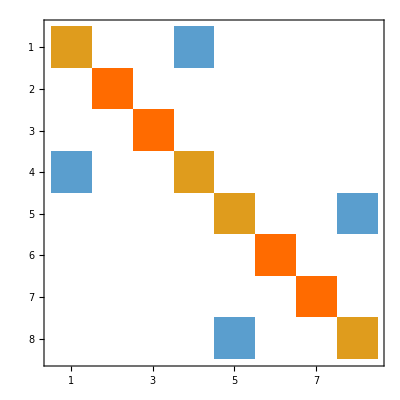

```mathematica
H = {{1,1},{1,2},{1,4},{1,5},{2,1},{2,2},{2,4},{2,5}};
B=Outer[sv, H,H,1]//Simplify;
B.B//FullSimplify//MatrixPlot
```

```mathematica
w=Exp[2Pi ⅈ/3];
```

```mathematica
M={{x w,0},{0,w^2(2P -x)}};
(Tr[M] // FullSimplify) //MatrixForm
Clear[x]
```

(-1)^(1/3) (-1-√5+x+(-1)^(1/3) x)

```mathematica
Solve[(-1)^(1/3) (-1-√5+x+(-1)^(1/3) x)==-P,x]//Simplify
```

{{x→1/2 (1+√5)}}

```mathematica
x^2 + (x-2)^2 +(-1 + 2x(2-x)) // Expand//Simplify
```

3

```mathematica
B={{b[1,1],b[1,2]},{b[2,1],2-b[1,1]}};
Reduce[{(Tr[B.B]//FullSimplify) ==-1},{b[1,1],b[1,2],b[2,1]},Complexes]
```

((b[1,1]==1/2 (2-ⅈ √6)||b[1,1]==1/2 (2+ⅈ √6))&&b[1,2]==0)||(b[1,2]≠0&&b[2,1]==(-5+4 b[1,1]-2 b[1,1]^2)/(2 b[1,2]))

```mathematica
B.B.B//Simplify//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
Reduce[FullSimplify[B.ConjugateTranspose[B]==IdentityMatrix[2]],{b[1,1],b[1,2]}]
```

Re[b[1,1]]==-1/2&&-(√3)/2<Im[b[1,1]]<(√3)/2&&(b[1,2]==-√(3/4-Im[b[1,1]]^2)||(-√(3/4-Im[b[1,1]]^2)<Re[b[1,2]]<√(3/4-Im[b[1,1]]^2)&&(Im[b[1,2]]==-√(3/4-Im[b[1,1]]^2-Re[b[1,2]]^2)||Im[b[1,2]]==√(3/4-Im[b[1,1]]^2-Re[b[1,2]]^2)))||b[1,2]==√(3/4-Im[b[1,1]]^2))

```mathematica
(2+w)/(w-1) - w^2//FullSimplify
```

0